## July 2020 - Revised calculations for ^135 Pr

## Computing the Triaxial Potential for the nucleus

## 3-axis

### Constants

```mathematica
j11=11/2;
spinValue=19/2;
```

### Formulas

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[Abs[ufct[I,a1,a2,a3,j,θ]]];
IF[moi_]:=1/(2*moi);
```

### Generate the q-values for plotting the potential

```mathematica
qValues=Table[q,{q,-8,8,0.1}];
fiValues[q_,k_]:=Table[JacobiAmplitude[q[[i]],k^2],{i,1,Length[q]}];
```

### Jacobi Functions - Functions for the elliptic variables

```mathematica
fiVar[q_,k_]:=JacobiAmplitude[q,k^2];
```

### Potential expression

```mathematica
vRotor[I_,q_,k_,v_]:=(I(I+1)k^2+v^2)Sin[fiVar[q,k]]^2+(2I+1)v*Cos[fiVar[q,k]]*√(1-k^2 Sin[fiVar[q,k]]^2);
rotorPlot[I_,i1_,i2_,i3_,j_,θ_]:=Plot[vRotor[I,q,kfct[I,IF[i1],IF[i2],IF[i3],j,θ],v0fct[I,IF[i1],IF[i2],j,θ]],{q,-8,8},AspectRatio->0.8,Frame->True,Axes->False,PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"q [rad]","V(q) [ℏ^2]"},(*PlotLegends->Placed[{"I=19/2"},{0.15,0.85}],*)FrameStyle->Directive[Black,Thick],Epilog->Inset[Style[StringTemplate["θ=(``)^o"][θ*180/π],18,Bold,Black,FontFamily->"Times New Roman"],Scaled[{0.5,0.15}]],FrameTicks->{{Automatic,None},{{-8,-4,0,4,8},None}},PlotRange->All];
```

### Create table with condition for the parameters: A and k must be positive

### Extra conditions for 3-axis: k=√(|u|), u<1,u>-1,|u|<1

## Conditions for u-factor

```mathematica
uTable[i1_,i2_,i3_,j_,θ_]:=Table[ufct[spin,IF[i1],IF[i2],IF[i3],j,θ*π/180],{spin,5.5,22.5,2}];
uValidity[i1_,i2_,i3_,j_,θ_]:=If[AllTrue[uTable[i1,i2,i3,j,θ],#<1&&#>-1&],{1,uTable[i1,i2,i3,j,θ]},{0,"FALSE"}];
uOptimalCondition[i1_,i2_,i3_,j_,θ_]:=If[uValidity[i1,i2,i3,j,θ][[1]]==1,1,0];
```

```mathematica
Manipulate[uValidity[i1,i2,i3,j11,θ],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{θ,-180,180,1}]
```

## Conditions for A-factor

```mathematica
ATable[i1_,i2_,i3_,j_,θ_]:=Table[Afct[spin,IF[i1],IF[i2],j,θ*π/180],{spin,5.5,22.5,2}];
AValidity[i1_,i2_,i3_,j_,θ_]:=If[AllTrue[ATable[i1,i2,i3,j,θ],#≥0&],{1,ATable[i1,i2,i3,j,θ]},{0,"FALSE"}];
AOptimalCondition[i1_,i2_,i3_,j_,θ_]:=If[AValidity[i1,i2,i3,j,θ][[1]]==1,1,0];
```

```mathematica
Manipulate[AValidity[i1,i2,i3,j11,θ],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{θ,-180,180,1}]
```

```mathematica
(*optimalCondition[a1_,a2_,a3_,j_,θ_]:=Table[If[Afct[spin,a1,a2,j,θ]≥0&&kfct[spin,a1,a2,a3,j,θ]≥0,1,0],{spin,5.5,22.5,2}];
checkParams[a1_,a2_,a3_,j_,θ_]:=If[AllTrue[optimalCondition[a1,a2,a3,j,θ],#==1&],1,"INVALID"];*)
```

### Only plot the triaxial potential if the parameters are consistent with the positivity condition of the inertial factor A and the constant factor k

```mathematica
(*potentialPlot[I_,a1_,a2_,a3_,j_,θ_]:=Plot[vRotor[I,q,kfct[I,a1,a2,a3,j,θ],v0fct[I,a1,a2,j,θ]],{q,-8,8},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameLabel->{"V(q) [ℏ^2]","q [rad]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},PlotStyle->{Thick,Red},AspectRatio->0.8];
plotOK[I_,a1_,a2_,a3_,j_,θ_]:=If[checkParams[a1,a2,a3,j,θ]==1,Show[potentialPlot[I,a1,a2,a3,j,θ]],"INVALID"];*)
```

## Valid (physical) plot for 3-axis quantization case V(q)

```mathematica
plotOK[I_,i1_,i2_,i3_,j_,θ_]:=If[uOptimalCondition[i1,i2,i3,j,θ]==1&&AOptimalCondition[i1,i2,i3,j,θ]==1,Show[rotorPlot[I,i1,i2,i3,j,θ*π/180]],"INVALID PLOT"];
```

```mathematica
Manipulate[plotOK[spin,i1,i2,i3,j11,θ],{spin,5.5,35.5,2},{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{θ,-180,180,1}]
```

## Potential good cases:

### I3-maximal moi:

#### Params: 30 15 60 11/2 -11

#### Potential

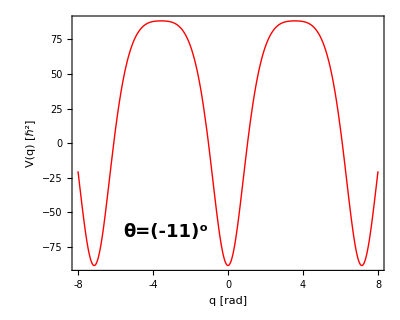

```mathematica
plotOK[30,15,60,j11,-11]
```

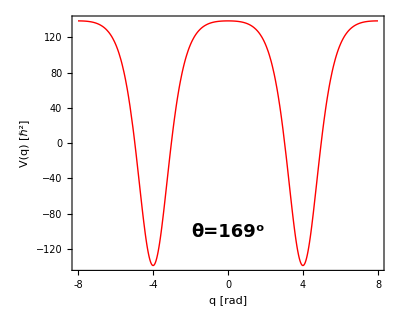

```mathematica
plotOK[30,15,60,j11,-11+180]
```